1.6×10^-19

8.85419×10^-12

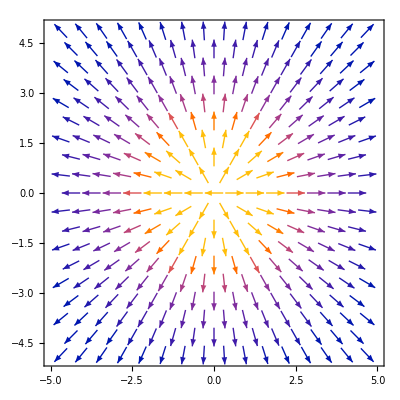
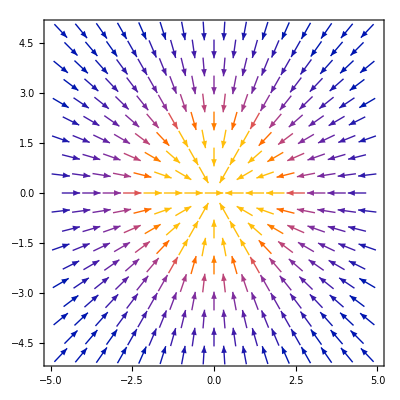

```mathematica
Q = 1.6*10^(-19)
d =8.854187822*10^(-12)

Ex[q_,x_,y_,x0_,y0_] := q/(4*Pi*d)*((x-x0)/((x-x0)^2+(y-y0)^2)^(1.5))
Ey[q_,x_,y_,x0_,y0_] := q/(4*Pi*d)*((y-y0)/((x-x0)^2+(y-y0)^2)^(1.5))

{VectorPlot[{Ex[Q,x,y,0,0],Ey[Q,x,y,0,0]},{x,-5,5},{y,-5,5}],VectorPlot[{Ex[-Q,x,y,0,0],Ey[-Q,x,y,0,0]},{x,-5,5},{y,-5,5}]}
```

(8.98755×10^9 q1 (x-x0))/(((x-x0)^2+(y-y0)^2)^1.5)+(8.98755×10^9 q2 (x-x1))/(((x-x1)^2+(y-y1)^2)^1.5)

(8.98755×10^9 q1 (y-y0))/(((x-x0)^2+(y-y0)^2)^1.5)+(8.98755×10^9 q2 (y-y1))/(((x-x1)^2+(y-y1)^2)^1.5)

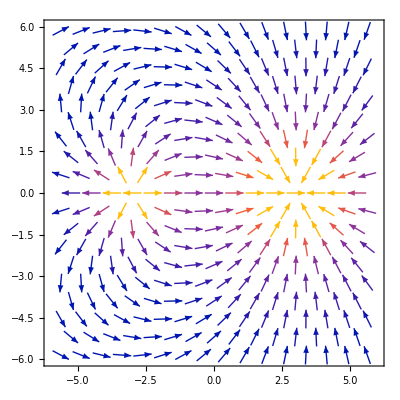

```mathematica
Exx[q1_,q2_,x_,y_,x0_,y0_,x1_,y1_] = Ex[q1,x,y,x0,y0] + Ex[q2,x,y,x1,y1]
Eyy[q1_,q2_,x_,y_,x0_,y0_,x1_,y1_]  = Ey[q1,x,y,x0,y0] + Ey[q2,x,y,x1,y1]

VectorPlot[{Exx[Q,-3*Q,x,y,-3,0,3,0],Eyy[Q,-3*Q,x,y,-3,0,3,0]},{x,-6,6},{y,-6,6}]
```

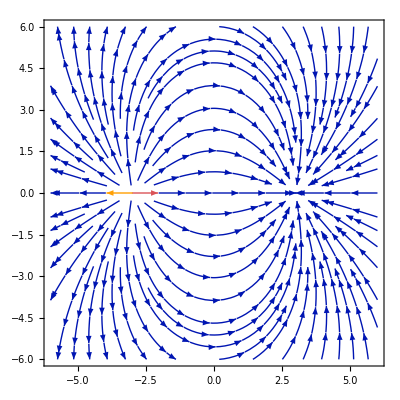

```mathematica
StreamPlot[{Exx[Q,-Q,x,y,-3,0,3,0],Eyy[Q,-Q,x,y,-3,0,3,0]},{x,-6,6},{y,-6,6}]
```

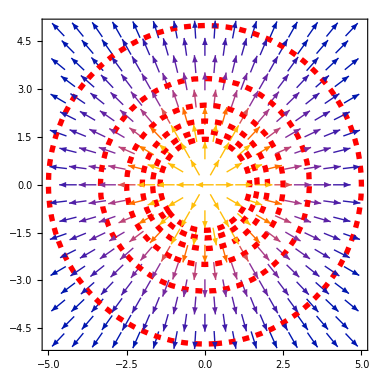

```mathematica
V[x_,y_,q_] := (1/Sqrt[x^2+y^2])
E1x[q_,x_,y_,x0_,y0_] :=((x-x0)/((x-x0)^2+(y-y0)^2)^(1.5))
E1y[q_,x_,y_,x0_,y0_] :=((y-y0)/((x-x0)^2+(y-y0)^2)^(1.5))

Show[VectorPlot[{E1x[Q,x,y,0,0],E1y[Q,x,y,0,0]},{x,-5,5},{y,-5,5}],
ContourPlot[V[x,y,Q] ,{x,-5,5},{y,-5,5}, ContourStyle->Directive[Red,Dashed,Thickness[0.01]],ContourShading->None]]
```

```mathematica
Plot3D[(x^2+y^2),{x,-3,3},{y,-3,3},PlotStyle->Texture[StreamPlot[Evaluate[D[(x^2+y^2),{{x,y}}]],{x,-3,3},{y,-3,3},Frame->None,ImageSize->Large]],Mesh->None,ImageSize->Large,PlotPoints->35]
```

-Graphics3D-

General::stop: Further output of StreamPlot::nonopt will be suppressed during this calculation.

```mathematica
μ = 4*Pi*10^(-7)
a=10
f[x_]:= (μ*a)/(2*Pi*x) 
g[x_]:= (μ *a*x)/(2*Pi)
```

π/2500000

10

10

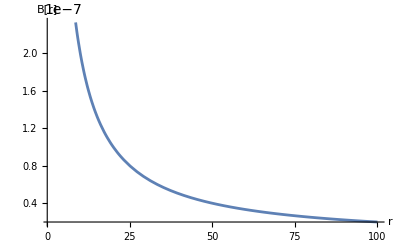

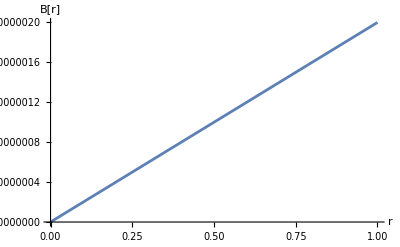

```mathematica
plot1 = Plot[f[x],{x,1,100},AxesLabel->{"r","B[r]"}]
plot2 = Plot[g[x],{x,0,1},AxesLabel->{"r","B[r]"}]
GraphicsGrid[{{plot2,plot1}},Frame->All, ImageSize->800]
```

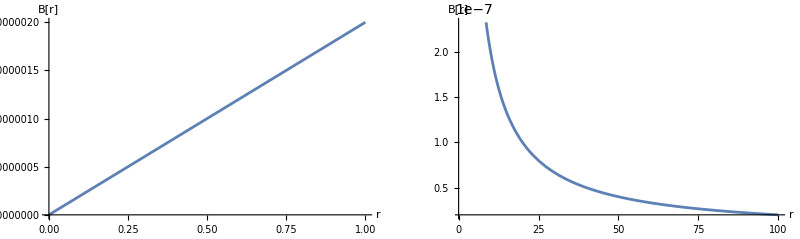

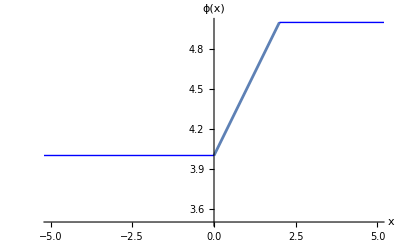

```mathematica
Show[
Plot[1/2x + 4 ,{x,0,2},PlotRange->{{-5,5},{3.5,5}},AxesLabel->{"x","ϕ(x)"}],
Graphics[{Blue,Thick,Line[{{2,5},{100,5}}]}],
Graphics[{Blue,Thick,Line[{{0,4},{-100,4}}]}]
]
```

1.47059×10^-7

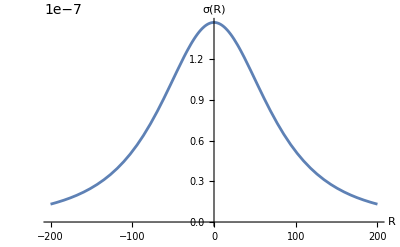

```mathematica
s[x_]:= 2/(4*3.4*(x^2 + 10000)^(3/2)) 
s[0]
Plot[s[x],{x,-200,200},AxesLabel->{"R","σ(R)"}]
```

```mathematica
VectorPlot3D[2/(4*Pi*r^3}]
```